/u/puchhamf/misc/workspace/ssj/data

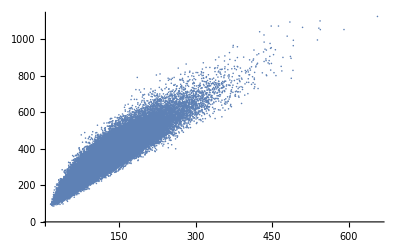

-Graphics3D-

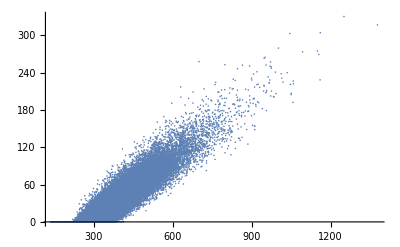

```mathematica
SetDirectory[NotebookDirectory[]]
dataRaw =Import["asian/MCData_Step_2.csv"];
n = 2^17;
data = RandomSample[dataRaw,n];
ListPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],PlotRange->All]
ListPointPlot3D[data,AxesLabel->{"S1","S2","Perf"},PlotRange->All]
fit = LinearModelFit[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],x,x];
ListPlot[Table[{fit[data[[i,1]]],data[[i,3]]},{i,1,n}],PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw1=Import["ReversibleIsometrization/MCData_Step_6.csv"];
dataRaw2=Import["ReversibleIsometrization/SobData_Step_6.csv"];
n = 2^17;
data1 = RandomSample[dataRaw1,n];
data2=RandomSample[dataRaw2,n];
ListPlot[{Table[{data1[[i,1]],data1[[i,2]]},{i,1,n}],Table[{data2[[i,1]],data2[[i,2]]},{i,1,n}]},PlotRange->All,PlotStyle->{Blue,Red}]
ListPointPlot3D[{data1,data2},AxesLabel->{"S1","S2","Perf"},PlotRange->All, PlotStyle->{Blue,Red}]
fit = LinearModelFit[Table[{data1[[i,1]],data1[[i,2]]},{i,1,n}],x,x];
(*LinearModelFit[Table[{data2[[i,1]],data2[[i,2]]},{i,1,n}],x,x];*)
 ListPlot[{Table[{fit[data1[[i,1]]],data1[[i,3]]},{i,1,n}],Table[{fit[data2[[i,1]]],data2[[i,3]]},{i,1,n}]},PlotRange->All,PlotStyle->{Blue,Red}]
```

-Graphics-

-Graphics3D-

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw =Import["SchloeglSystem/MCData_Step_10.csv"];
n = 2^17;
data = RandomSample[dataRaw,n];
dataProj = Table[{data[[i,1]],data[[i,2]],data[[i,3]]},{i,1,n}];
fit = LinearModelFit[dataProj,{1,x,y},{x,y}];
dataProjFit = Table[{data[[i,1]],data[[i,2]],fit[data[[i,1]],data[[i,2]]]},{i,1,n}];
ListPointPlot3D[{dataProj,dataProjFit},PlotStyle->{{Blue,PointSize[Medium]},{Red,PointSize[Medium]}},PlotRange->All, AxesLabel->{"S1","S2","S3"},PlotLabel->S3 == fit[S1,S2],ImageSize->Large]
dataPlot = Table[{data[[i,1]],fit[data[[i,1]],data[[i,2]]],data[[i,4]]},{i,1,n}];
ff =  Fit[dataPlot,{1,x,y,x y, x^2y,x y^2,x^2,y^2,x ^3,y^3},{x,y}];
ffit [x_,y_]=ff;
dataPlot2 = Table[{dataPlot[[i,1]],dataPlot[[i,2]],ffit[dataPlot[[i,1]],dataPlot[[i,2]]]},{i,1,Length[dataPlot]}];
(*ListPlot3D[{dataPlot,dataPlot2},PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->FullSimplify[ff],AxesLabel->{"S1", "S3","performance"}]*)
ListPointPlot3D[{dataPlot,dataPlot2},PlotRange->All,PlotStyle->{{Blue,PointSize[Small]},{Red,PointSize[Medium]}},PlotLabel->Pane[FullSimplify[ff],{1000,All}],AxesLabel->{"S1", "S3","performance"},ImageSize->Large]
```

-Graphics3D-

-Graphics3D-